# The Scattering of Light By Light

This tutorial will illustrate a few strategies you can employ to streamline complex calculations with Package-X by using the scattering of light by light in quantum electrodynamics as an example.  We will aim to calculate the scattering amplitude and differential cross section.  In certain kinematic limits, compact analytic expressions exist and can be quickly obtained.  Otherwise, the general result with full kinematic dependence is extremely complicated, and can take a long time to calculate. But with clever strategies it can be obtained in a reasonable amount of time, and can even be numerically evaluated.  We will also save the final result so it can be reloaded upon restarting Mathematica.

## Setup

At leading order, the Feynman diagrams are:

"TraditionalForm`s-channel" | "TraditionalForm`t-channel" | "TraditionalForm`u-channel"
 |  | 
 |  |

In all diagrams, the internal fermions are electron lines, with their momenta directed with the flow of charge.  The QED vertex factor is:

= i e γ^μ

By charge conjugation invariance of QED, each diagram in the second row contributes the same as the diagram above it.  Therefore, we only need to add the first three diagrams and multiply the result by 2.  We will parametrize the amplitude as:

i ℳ=[2 Π_(s)+2 Π_(t)+2 Π_(u)]^μνρσ ϵ_μ(p_1)ϵ_ν(p_2)ϵ_ρ^*(p_3)ϵ_σ^*(p_4)

where the individual contributions are

Π_(s)^μνρσ=-e^4 μ^(2ϵ)∫(ⅆ^d k)/(2π)^d Tr[γ^μ(k.γ+m)γ^ν((k-p_2).γ+m)γ^σ((k+p_1-p_3).γ)γ^ρ((k+p_1).γ+m)]/([k^2-m^2][(k-p_2)^2-m^2][(k+p_1-p_3)^2-m^2][(k+p_1)^2-m^2])

Π_(t)^μνρσ=-e^4 μ^(2ϵ)∫(ⅆ^d k)/(2π)^d Tr[γ^μ(k.γ+m)γ^σ((k+p_1+p_2-p_3).γ+m)γ^ν((k+p_1-p_3).γ)γ^ρ((k+p_1).γ+m)]/([k^2-m^2][(k+p_1+p_2-p_3)^2-m^2][(k+p_1-p_3)^2-m^2][(k+p_1)^2-m^2])

Π_(u)^μνρσ=-e^4 μ^(2ϵ)∫(ⅆ^d k)/(2π)^d Tr[γ^μ(k.γ+m)γ^ν((k-p_2).γ+m)γ^ρ((k-p_2+p_3).γ)γ^σ((k+p_1).γ+m)]/([k^2-m^2][(k-p_2)^2-m^2][(k-p_2+p_3)^2-m^2][(k+p_1)^2-m^2]),

subject to the on shell kinematic conditions p_1^2=p_2^2=p_3^2=p_4^2=0, s=(p_1+p_2)^2, and t=(p_1-p_3)^2.
The external photon polarization vectors which contract into the loop integrals satisfy transversality p.ϵ(p)=0.  Therefore, it is safe to set p_1^μ=p_2^ν=p_3^ρ=p_4^σ=0 in the result.

Define on shell conditions and photon polarization transversality conditions:

```mathematica
Needs["X`"]
onShell=MandelstamRelations[{p1,p2,p3,p4,0,0,0,0}->{s,t,u},Eliminate->u]
```

{p1.p1→0,p2.p2→0,p3.p3→0,p4.p4→0,p1.p2→s/2,p3.p4→s/2,p1.p3→-t/2,p2.p4→-t/2,p1.p4→(s+t)/2,p2.p3→(s+t)/2,ε_({p1},{p2},{p3},{p4})→0}

```mathematica
photonTransversality={Subscript[p1, μ]->0,Subscript[p2, ν]->0,Subscript[p3, ρ]->0,Subscript[p4, σ]->0}
```

{p1_μ→0,p2_ν→0,p3_ρ→0,p4_σ→0}

Initiate the integrals (omitting the factor -e^4), and apply the on shell conditions:

```mathematica
sChannelGraph=LoopIntegrate[Spur[Subscript[γ, μ],k.γ+m 𝟙,Subscript[γ, ν],(k-p2).γ+m 𝟙,Subscript[γ, σ],(k+p1-p3).γ+m 𝟙,Subscript[γ, ρ],(k+p1).γ+m 𝟙],k,{k,m},{k+p1,m},{k+p1-p3,m},{k-p2,m}]/.onShell/.photonTransversality;
tChannelGraph=LoopIntegrate[Spur[Subscript[γ, μ],k.γ+m 𝟙,Subscript[γ, σ],(k+p1-p3+p2).γ+m 𝟙,Subscript[γ, ν],(k+p1-p3).γ+m 𝟙,Subscript[γ, ρ],(k+p1).γ+m 𝟙],k,{k,m},{k+p1,m},{k+p1-p3,m},{k+p1-p3+p2,m}]/.onShell/.photonTransversality;
uChannelGraph=LoopIntegrate[Spur[Subscript[γ, μ],k.γ+m 𝟙,Subscript[γ, ν],(k-p2).γ+m 𝟙,Subscript[γ, ρ],(k+p3-p2).γ+m 𝟙,Subscript[γ, σ],(k+p1).γ+m 𝟙],k,{k,m},{k+p1,m},{k+p3-p2,m},{k-p2,m}]/.onShell/.photonTransversality;

total=(2sChannelGraph+2tChannelGraph+2uChannelGraph);
```

## Properties of the photon-photon scattering amplitude

The one loop photon-photon scattering amplitude satisfies a number of properties which can be used to check the calculation.

### Ultraviolet behavior

The four photon Green function is expected to be ultraviolet finite.

Apply LoopRefine with the option Part→UVDivergent to compute only the ultraviolet divergent part of the total amplitude.  Considered separately, each diagram is divergent.

```mathematica
LoopRefine[sChannelGraph,Part->UVDivergent]
LoopRefine[tChannelGraph,Part->UVDivergent]
LoopRefine[uChannelGraph,Part->UVDivergent]
```

(4 𝕘_(σ,ρ) 𝕘_(μ,ν))/(3 ϵ)+(4 𝕘_(σ,ν) 𝕘_(μ,ρ))/(3 ϵ)-(8 𝕘_(σ,μ) 𝕘_(ν,ρ))/(3 ϵ)

-(8 𝕘_(σ,ρ) 𝕘_(μ,ν))/(3 ϵ)+(4 𝕘_(σ,ν) 𝕘_(μ,ρ))/(3 ϵ)+(4 𝕘_(σ,μ) 𝕘_(ν,ρ))/(3 ϵ)

(4 𝕘_(σ,ρ) 𝕘_(μ,ν))/(3 ϵ)-(8 𝕘_(σ,ν) 𝕘_(μ,ρ))/(3 ϵ)+(4 𝕘_(σ,μ) 𝕘_(ν,ρ))/(3 ϵ)

The total amplitude is UV finite:

```mathematica
LoopRefine[total,Part->UVDivergent]
```

0

### QED Ward identities

The scattering amplitude is expected to satisfy the on shell Ward identity
at each of the four vertices

{[2 Π_(s)+2 Π_(t)+2 Π_(u)]^μνρσ (p_1)_μ=0
[2 Π_(s)+2 Π_(t)+2 Π_(u)]^μνρσ (p_2)_ν=0
[2 Π_(s)+2 Π_(t)+2 Π_(u)]^μνρσ (p_3)_ρ=0
[2 Π_(s)+2 Π_(t)+2 Π_(u)]^μνρσ (p_4)_σ=0

Contract the result with tensors p1_μ, p2_ν, p3_ρ, and p4_σ, apply the on shell conditions and photon transversality condition apply LoopRefine (about a minute runtime to verify all four identities on a modern machine):

```mathematica
LoopRefine[Contract[total Subscript[p1, μ]]/.onShell]
LoopRefine[Contract[total Subscript[p2, ν]]/.onShell]
LoopRefine[Contract[total Subscript[p3, ρ]]/.onShell]
LoopRefine[Contract[total Subscript[p4, σ]]/.p4->p1+p2-p3/.onShell/.photonTransversality]
```

0

0

0

«1 more identical outputs»

It is more efficient to verify these by directly contracting the integrands before calling LoopIntegrate (checking p1_μ Ward identity):

```mathematica
sChannelWardP1=LoopIntegrate[Contract[Subscript[p1, μ] Spur[Subscript[γ, μ],k.γ+m 𝟙,Subscript[γ, ν],(k-p2).γ+m 𝟙,Subscript[γ, σ],(k+p1-p3).γ+m 𝟙,Subscript[γ, ρ],(k+p1).γ+m 𝟙]],k,{k,m},{k+p1,m},{k+p1-p3,m},{k-p2,m}]/.onShell/.photonTransversality;
tChannelWardP1=LoopIntegrate[Contract[Subscript[p1, μ] Spur[Subscript[γ, μ],k.γ+m 𝟙,Subscript[γ, σ],(k+p1-p3+p2).γ+m 𝟙,Subscript[γ, ν],(k+p1-p3).γ+m 𝟙,Subscript[γ, ρ],(k+p1).γ+m 𝟙]],k,{k,m},{k+p1,m},{k+p1-p3,m},{k+p1-p3+p2,m}]/.onShell/.photonTransversality;
uChannelWardP1=LoopIntegrate[Contract[Subscript[p1, μ] Spur[Subscript[γ, μ],k.γ+m 𝟙,Subscript[γ, ν],(k-p2).γ+m 𝟙,Subscript[γ, ρ],(k+p3-p2).γ+m 𝟙,Subscript[γ, σ],(k+p1).γ+m 𝟙]],k,{k,m},{k+p1,m},{k+p3-p2,m},{k-p2,m}]/.onShell/.photonTransversality;

LoopRefine[sChannelWardP1+tChannelWardP1+uChannelWardP1]
```

0

### Ward identities in Mathematica 10 and above

Mathematica 10 features a new evaluation control function Inactive which stops functions from evaluating until they are enabled with Activate.  We can use this feature to check the Ward identities with ease:

```mathematica
sChannelGraph=Inactive[LoopIntegrate][Inactive[Spur][Subscript[γ, μ],k.γ+m 𝟙,Subscript[γ, ν],(k-p2).γ+m 𝟙,Subscript[γ, σ],(k+p1-p3).γ+m 𝟙,Subscript[γ, ρ],(k+p1).γ+m 𝟙],k,{k,m},{k+p1,m},{k+p1-p3,m},{k-p2,m}]
tChannelGraph=Inactive[LoopIntegrate][Inactive[Spur][Subscript[γ, μ],k.γ+m 𝟙,Subscript[γ, σ],(k+p1-p3+p2).γ+m 𝟙,Subscript[γ, ν],(k+p1-p3).γ+m 𝟙,Subscript[γ, ρ],(k+p1).γ+m 𝟙],k,{k,m},{k+p1,m},{k+p1-p3,m},{k+p1-p3+p2,m}]
uChannelGraph=Inactive[LoopIntegrate][Inactive[Spur][Subscript[γ, μ],k.γ+m 𝟙,Subscript[γ, ν],(k-p2).γ+m 𝟙,Subscript[γ, ρ],(k+p3-p2).γ+m 𝟙,Subscript[γ, σ],(k+p1).γ+m 𝟙],k,{k,m},{k+p1,m},{k+p3-p2,m},{k-p2,m}]
```

```mathematica
Activate[Contract[Subscript[p1, μ](sChannelGraph+tChannelGraph+uChannelGraph)]]/.onShell/.photonTransversality//LoopRefine
```

```mathematica
Activate[Contract[Subscript[p2, ν](sChannelGraph+tChannelGraph+uChannelGraph)]]/.onShell/.photonTransversality//LoopRefine
```

```mathematica
Activate[Contract[Subscript[p3, ρ](sChannelGraph+tChannelGraph+uChannelGraph)]]/.onShell/.photonTransversality//LoopRefine
```

```mathematica
Activate[Contract[(*p4*)Subscript[(p1+p2-p3), σ](sChannelGraph+tChannelGraph+uChannelGraph)]]/.onShell/.photonTransversality//LoopRefine
```

## Scattering amplitude in various limits

With Package-X, we can compute the light by light scattering amplitude in different kinematic limits.  Remember to restore the omitted factor -e^4, and the factor i/(16 π^2) implicit in the normalization of LoopIntegrate.

### Low energy (Euler-Heisenberg) limit

In the low energy limit s,|t|≪m, the amplitude starts at 𝒪(1/m^4):

Use LoopRefineSeries to obtain the large electron mass behavior of the amplitude (about 15 seconds runtime on a modern machine):

```mathematica
ampLE=LoopRefineSeries[total,{m,Infinity,4}]//Normal
```

1/m^4(36/35 p1_σ p1_ν p1_ρ p2_μ+36/35 p1_ν p1_ρ p2_σ p2_μ+52/105 p1_σ p1_ν p2_μ p2_ρ+52/105 p1_ν p2_σ p2_μ p2_ρ-16/21 p1_ν p1_ρ p2_μ p3_σ-8/35 p1_ν p2_μ p2_ρ p3_σ-36/35 p1_σ p1_ν p1_ρ p3_μ-16/21 p1_ν p1_ρ p2_σ p3_μ-352/315 p1_σ p1_ν p2_ρ p3_μ-352/315 p1_ν p2_σ p2_ρ p3_μ+36/35 p1_ν p1_ρ p3_σ p3_μ+352/315 p1_ν p2_ρ p3_σ p3_μ-4/105 (27 p1_ρ+13 p2_ρ) (p1_σ+p2_σ-p3_σ) (p2_μ-p3_μ) (p1_ν-p3_ν)-104/63 p1_σ p1_ρ p2_μ p3_ν-104/63 p1_ρ p2_σ p2_μ p3_ν-8/35 p1_σ p2_μ p2_ρ p3_ν-52/105 p2_σ p2_μ p2_ρ p3_ν+104/63 p1_ρ p2_μ p3_σ p3_ν+52/105 p2_μ p2_ρ p3_σ p3_ν+36/35 p1_σ p1_ρ p3_μ p3_ν+16/21 p1_ρ p2_σ p3_μ p3_ν+8/35 p1_σ p2_ρ p3_μ p3_ν+52/105 p2_σ p2_ρ p3_μ p3_ν-36/35 p1_ρ p3_σ p3_μ p3_ν-52/105 p2_ρ p3_σ p3_μ p3_ν-28/45 (s+t) p1_ν p1_ρ 𝕘_(σ,μ)-28/45 t p1_ν p2_ρ 𝕘_(σ,μ)+28/45 s p1_ρ p3_ν 𝕘_(σ,μ)-2/15 (s+t) p2_ρ p3_ν 𝕘_(σ,μ)+28/45 (s+t) p1_ρ p2_μ 𝕘_(σ,ν)+28/45 t p2_μ p2_ρ 𝕘_(σ,ν)+2/15 t p1_ρ p3_μ 𝕘_(σ,ν)+28/45 s p2_ρ p3_μ 𝕘_(σ,ν)-2/15 s p1_ν p2_μ 𝕘_(σ,ρ)-28/45 (s+t) p1_ν p3_μ 𝕘_(σ,ρ)+28/45 t p2_μ p3_ν 𝕘_(σ,ρ)+28/45 s p3_μ p3_ν 𝕘_(σ,ρ)+14/45 (s+t) p1_σ p1_ρ 𝕘_(μ,ν)-14/45 (s+t) p1_ρ p2_σ 𝕘_(μ,ν)+14/45 t p1_σ p2_ρ 𝕘_(μ,ν)-14/45 t p2_σ p2_ρ 𝕘_(μ,ν)-2/45 (10 s+7 t) p1_ρ p3_σ 𝕘_(μ,ν)-2/45 (3 s-7 t) p2_ρ p3_σ 𝕘_(μ,ν)+1/45 (3 s^2-14 s t-14 t^2) 𝕘_(σ,ρ) 𝕘_(μ,ν)+14/45 (s+t) p1_σ p1_ν 𝕘_(μ,ρ)+2/45 (7 s+10 t) p1_ν p2_σ 𝕘_(μ,ρ)+14/45 (s+t) p1_ν p3_σ 𝕘_(μ,ρ)-14/45 s p1_σ p3_ν 𝕘_(μ,ρ)+2/45 (7 s-3 t) p2_σ p3_ν 𝕘_(μ,ρ)-14/45 s p3_σ p3_ν 𝕘_(μ,ρ)+1/45 (-14 s^2-14 s t+3 t^2) 𝕘_(σ,ν) 𝕘_(μ,ρ)-2/45 (3 s+10 t) p1_σ p2_μ 𝕘_(ν,ρ)-14/45 t p2_σ p2_μ 𝕘_(ν,ρ)-14/45 t p2_μ p3_σ 𝕘_(ν,ρ)+2/45 (10 s+3 t) p1_σ p3_μ 𝕘_(ν,ρ)-14/45 s p2_σ p3_μ 𝕘_(ν,ρ)-14/45 s p3_σ p3_μ 𝕘_(ν,ρ)+1/45 (3 s^2+20 s t+3 t^2) 𝕘_(σ,μ) 𝕘_(ν,ρ))

### High energy/large momentum transfer limit

In the high energy limit s,|t|≫m, the electron mass is negligible.

Make the replacement m→0 and call LoopRefine (about 20 seconds runtime on a modern machine):

```mathematica
ampHE=LoopRefine[total/.m->0,TargetScale->√-t]
```

(32/s^2+(16 π^2 (s^2+3 s t+2 t^2))/s^4+(64 (s+t) Log[-t/(s+t)])/s^3+(16 (s^2+3 s t+2 t^2) Log[-t/(s+t)]^2)/s^4) p1_σ p1_ν p1_ρ p2_μ+((32 (s+t))/(s^2 t)+(16 π^2 (s^2+3 s t+2 t^2))/s^4+(64 (s+t) Log[-t/(s+t)])/s^3+(16 (s^2+3 s t+2 t^2) Log[-t/(s+t)]^2)/s^4) p1_ν p1_ρ p2_σ p2_μ+«54»+(-8/3+(2 π^2 (2 s^6-9 s^4 t^2-16 s^3 t^3-9 s^2 t^4+2 t^6))/(3 s^2 t^2 (s+t)^2)+(4 s (s^3-3 s t^2-3 t^3) Log[t/s]^2)/(3 t^2 (s+t)^2)+(8 (s^2-s t+t^2) Log[-t/(s+t)])/(3 s t)+(4 (s^4-2 s^3 t-3 s^2 t^2-2 s t^3+t^4) Log[-t/(s+t)]^2)/(3 s^2 t^2)+Log[t/s] (-(8 s^2)/(3 t (s+t))+(4 (-2 s^2+4 s t+3 t^2) Log[-t/(s+t)])/(3 t^2))) 𝕘_(σ,μ) 𝕘_(ν,ρ)

In the massless limit, individual Passarino-Veltman funcions contributing to the amplitude are infrared divergent.  However the divergences cancel in the total, can can be checked by the absence of 1/ϵ poles:

```mathematica
FreeQ[ampHE,ϵ]
```

True

### Forward scattering limit

In the forward limit p_1=p_3 and p_2=p_4 so that t=0.  By photon polarization transversality, p_1^ρ and p_2^σ can be set to zero.

Make the replacement p3→p1, p4→p2, t→0, p1_ρ→0 and p2_σ→0.  Call LoopRefine to calculate (about 15 seconds runtime on a modern machine):

```mathematica
ampFor=LoopRefine[total/.{t->0,p3->p1,p4->p2}/.{Subscript[p1, ρ]->0,Subscript[p2, σ]->0}]
```

p1_σ p1_ν p2_μ p2_ρ (-32/s^2-(64 m^2 DiscB[-s,m,m])/s^3+(64 m^2 DiscB[s,m,m])/s^3+(128 m^4 ScalarC0[0,0,-s,m,m,m])/s^3-(128 m^4 ScalarC0[0,0,s,m,m,m])/s^3)+p1_σ p1_μ p1_ν p2_ρ (16/s^2+(16 (2 m^2+3 s) DiscB[-s,m,m])/s^3-(16 (2 m^2+3 s) DiscB[s,m,m])/s^3-(16 (4 m^4+s^2) ScalarC0[0,0,-s,m,m,m])/s^3-(16 (-4 m^4+s^2) ScalarC0[0,0,s,m,m,m])/s^3)+p1_ν p2_ρ 𝕘_(σ,μ) (8/s+(8 (2 m^2+3 s) DiscB[-s,m,m])/s^2-(8 (2 m^2+3 s) DiscB[s,m,m])/s^2-(8 (4 m^4+s^2) ScalarC0[0,0,-s,m,m,m])/s^2-(8 (-4 m^4+s^2) ScalarC0[0,0,s,m,m,m])/s^2)+p1_σ p2_μ 𝕘_(ν,ρ) (8/s+(8 (2 m^2+3 s) DiscB[-s,m,m])/s^2-(8 (2 m^2+3 s) DiscB[s,m,m])/s^2-(8 (4 m^4+s^2) ScalarC0[0,0,-s,m,m,m])/s^2-(8 (-4 m^4+s^2) ScalarC0[0,0,s,m,m,m])/s^2)+p1_σ p1_μ 𝕘_(ν,ρ) (-8/s-(8 (2 m^2+3 s) DiscB[-s,m,m])/s^2+(8 (2 m^2+3 s) DiscB[s,m,m])/s^2+(8 (4 m^4+s^2) ScalarC0[0,0,-s,m,m,m])/s^2+(8 (-4 m^4+s^2) ScalarC0[0,0,s,m,m,m])/s^2)+𝕘_(σ,μ) 𝕘_(ν,ρ) (-4-(4 (2 m^2+3 s) DiscB[-s,m,m])/s+(4 (2 m^2+3 s) DiscB[s,m,m])/s+(4 (4 m^4+s^2) ScalarC0[0,0,-s,m,m,m])/s+(4 (-4 m^4+s^2) ScalarC0[0,0,s,m,m,m])/s)+p1_ν p2_μ 𝕘_(σ,ρ) (8/s+(8 (2 m^2-3 s) DiscB[-s,m,m])/s^2+(8 (-2 m^2+3 s) DiscB[s,m,m])/s^2+(8 (-4 m^4+s^2) ScalarC0[0,0,-s,m,m,m])/s^2+(8 (4 m^4+s^2) ScalarC0[0,0,s,m,m,m])/s^2)+p1_σ p2_ρ 𝕘_(μ,ν) (8/s+(8 (2 m^2-3 s) DiscB[-s,m,m])/s^2+(8 (-2 m^2+3 s) DiscB[s,m,m])/s^2+(8 (-4 m^4+s^2) ScalarC0[0,0,-s,m,m,m])/s^2+(8 (4 m^4+s^2) ScalarC0[0,0,s,m,m,m])/s^2)+𝕘_(σ,ρ) 𝕘_(μ,ν) (-4+(4 (-2 m^2+3 s) DiscB[-s,m,m])/s+(4 (2 m^2-3 s) DiscB[s,m,m])/s-(4 (-4 m^4+s^2) ScalarC0[0,0,-s,m,m,m])/s-(4 (4 m^4+s^2) ScalarC0[0,0,s,m,m,m])/s)+p1_μ p2_ρ 𝕘_(σ,ν) (-56/s+(8 (2 m^2-s) DiscB[-s,m,m])/s^2-(8 (2 m^2+s) DiscB[s,m,m])/s^2+(8 (-4 m^4-4 m^2 s+s^2) ScalarC0[0,0,-s,m,m,m])/s^2-(8 (-4 m^4+4 m^2 s+s^2) ScalarC0[0,0,s,m,m,m])/s^2)+𝕘_(σ,ν) 𝕘_(μ,ρ) (28+(4 (-2 m^2+s) DiscB[-s,m,m])/s+(4 (2 m^2+s) DiscB[s,m,m])/s-(4 (-4 m^4-4 m^2 s+s^2) ScalarC0[0,0,-s,m,m,m])/s+(4 (-4 m^4+4 m^2 s+s^2) ScalarC0[0,0,s,m,m,m])/s)

### General case

Apply LoopRefine on the full amplitude (about 40 seconds runtime on a modern machine):

```mathematica
fullAmplitude=LoopRefine[total]
```

p2_σ p2_ρ p3_μ p3_ν (-(32 s)/(t (s+t)^2)+(64 s DiscB[s,m,m])/(s+t)^3-(64 s DiscB[t,m,m])/(s+t)^3-(32 s (m^2 s^2-2 m^2 s t-s^2 t-3 m^2 t^2+s t^2) ScalarC0[0,0,s,m,m,m])/(t (s+t)^4)+(32 «2» ScalarC0[0,0,«3»,m])/(s t (s+t))-(32 (2 m^2 s^4+«6»+2 m^2 t^4) ScalarC0[0,0,t,m,m,m])/(s t (s+t)^4)+(16 m^2 (-s^2+4 m^2 t-s t) ScalarD0[0,0,0,0,s,-s-t,m,m,m,m])/(t (s+t)^2)+(16 (4 m^4 s^2+3 m^2 s^3+8 m^4 s t-2 m^2 s^2 t-s^3 t+4 m^4 t^2-5 m^2 s t^2+s^2 t^2) ScalarD0[0,0,0,0,s,t,m,m,m,m])/(s+t)^4+(16 m^2 (4 m^2 s-s^2-3 s t-2 t^2) ScalarD0[0,0,0,0,-s-t,t,m,m,m,m])/(s (s+t)^2))+«1»+«54»+«1»

## Unpolarized differential cross section

The tensor algebraic capabilities of Package-X can also aid in the evaluation of the unpolarized differential cross section.  Below, the cross section will be calculated in three kinematic cases: the low energy limit, the high energy limit, and the general case.

The unpolarized photon-photon differential cross section is given by:

OverBar[dσ]=1/Flux|ℳ̄|^2 d(PS),

where Flux=2s and d(PS)=1/(32 π^2)dΩ.

To obtain the matrix element squared |ℳ̄|^2, the complex conjugate of the matrix element is needed,

i ℳ=[2 Π_(s)+2 Π_(t)+2 Π_(u)]^μνρσ ϵ_μ(p_1)ϵ_ν(p_2)ϵ_ρ^*(p_3)ϵ_σ^*(p_4)

(i ℳ)^*=[2 Π_(s)^*+2 Π_(t)^*+2 Π_(u)^*]^μνρσ  ϵ_μ^*(p_1)ϵ_ν^*(p_2)ϵ_ρ(p_3)ϵ_σ(p_4).

After multiplying, average over the initial and sum over final photon polarizations using

∑ϵ_α^*(p_1) ϵ_β(p_1) ⟶ -ℊ_αβ+(vanishing)

valid for amplitudes satisfying the Ward identity.  Then, the matrix element squared is:

|ℳ̄|^2=((1/4[2 Π_(s)+2 Π_(t)+2 Π_(u)])^μνρσ[2 Π_(s)^*+2 Π_(t)^*+2 Π_(u)^*])_μνρσ .

### Low energy (Euler-Heisenberg) limit

Since the scattering amplitude in the low energy limit is purely real (below all physical threshold), no complex conjugation is needed.  The spin-averaged matrix element squared and therefore the differential cross section are readily obtained.

Contract the product of the low energy amplitude with itself, and apply the on shell kinematic conditions.  The factor |-e^4 i/(16 π^2)|^2 has been restored:

```mathematica
(e^4/(16 π^2))^2 Contract[1/4 ampLE*ampLE]/.onShell//Simplify
ampSqLE=%/.𝒹->4
```

((578-503 𝒹+107 𝒹^2) e^8 (s^2+s t+t^2)^2)/(1036800 m^8 π^4)

(139 e^8 (s^2+s t+t^2)^2)/(518400 m^8 π^4)

Multiply by the flux and phase space factors to obtain the differential cross section:

```mathematica
dσdΩLE[α_,s_,t_]=1/(2s)ampSqLE 1/(32 π^2)/.e->√(α 4π)
```

(139 (s^2+s t+t^2)^2 α^4)/(129600 m^8 π^2 s)

```mathematica
(*In the center-of-mass frame,
ω=Angular frequency of each incident photon,
θ=COM scattering angle *)
%/.t->-1/(2s)Kallenλ[0,0,s](1-Cos[θ])/.s->4 ω^2//FactorSquareFree
```

(139 α^4 ω^6 (3+Cos[θ]^2)^2)/(32400 m^8 π^2)

### High energy/large momentum transfer limit

In the high energy limit, the amplitude is complex, with the imaginary parts arising from the various logarithmic factors.  After selectively extracting the imaginary parts, the conjugate amplitude is constructed from which the cross section follows.

Use Cases and DeleteDuplicates to construct a list of the logarithmic factors appearing in the high energy scattering amplitude:

```mathematica
Cases[ampHE,_Log,Infinity]//DeleteDuplicates
```

{Log[-t/(s+t)],Log[t/s]}

In the physical region (s>0, t>0 and s+t<0), only the ln(t/s) logs give an imaginary part.  Define the amplitude and its conjugate by explictly separating the imaginary part from the logarithms:

```mathematica
ampHEx=ampHE/.Log[t/s]->Log[Abs[t/s]]+ⅈ π;
ampHEcc=ampHE/.Log[t/s]->Log[Abs[t/s]]-ⅈ π;
```

Contract the product of the low energy amplitude with itself, and apply the on shell kinematic conditions.  Collect the result by the various logarithmic factors, and Simplify each coefficient.

```mathematica
ampSqHE=(e^4/(16 π^2))^2 Collect[Contract[1/4 ampHEx*ampHEcc]/.onShell/.𝒹->4,_Log,Simplify]
```

1/(256 π^4)e^8 (1/(s^4 t^2 (s+t)^2)8 (32 s^4 t^2 (s+t)^2+π^4 t^2 (s^3+3 s^2 t+4 s t^2+2 t^3)^2+4 π^2 s^2 (4 s^6+12 s^5 t+15 s^4 t^2+8 s^3 t^3+9 s^2 t^4+6 s t^5+2 t^6))+(16 (2 s^8+4 s^7 t+4 s^6 t^2+2 s^5 t^3+s^4 t^4+2 s^3 t^5+4 s^2 t^6+4 s t^7+2 t^8) Log[-t/(s+t)]^4)/(s^4 t^4)-(128 (s^2+s t+t^2) (t^2 (s+t)^2+π^2 (2 s^4+7 s^3 t+8 s^2 t^2+2 s t^3+t^4)) Log[Abs[t/s]])/(t^3 (s+t)^3)+1/(t^4 (s+t)^4)64 (t^2 (s+t)^2 (3 s^4+9 s^3 t+11 s^2 t^2+4 s t^3+2 t^4)+π^2 (2 s^8+12 s^7 t+32 s^6 t^2+50 s^5 t^3+51 s^4 t^4+34 s^3 t^5+16 s^2 t^6+4 s t^7+t^8)) Log[Abs[t/s]]^2-(64 (2 s^6+9 s^5 t+17 s^4 t^2+17 s^3 t^3+11 s^2 t^4+3 s t^5+t^6) Log[Abs[t/s]]^3)/(t^3 (s+t)^3)+1/(t^4 (s+t)^4)16 (2 s^8+12 s^7 t+32 s^6 t^2+50 s^5 t^3+51 s^4 t^4+34 s^3 t^5+16 s^2 t^6+4 s t^7+t^8) Log[Abs[t/s]]^4+Log[-t/(s+t)]^3 ((64 (2 s^6+3 s^5 t+2 s^4 t^2+s^3 t^3+2 s^2 t^4+3 s t^5+2 t^6))/(s^3 t^3)-(32 (2 s^2+2 s t+t^2)^2 Log[Abs[t/s]])/t^4)+Log[-t/(s+t)]^2 (1/(s^4 t^4)16 (4 s^2 t^2 (3 s^4+3 s^3 t+2 s^2 t^2+3 s t^3+3 t^4)+π^2 (8 s^8+16 s^7 t+16 s^6 t^2+8 s^5 t^3+3 s^4 t^4+4 s^3 t^5+8 s^2 t^6+8 s t^7+4 t^8))-(96 (4 s^3+6 s^2 t+4 s t^2+t^3) Log[Abs[t/s]])/t^3+(48 (2 s^2+2 s t+t^2)^2 Log[Abs[t/s]]^2)/t^4)+Log[-t/(s+t)] ((32 (4 s^2 t^2 (s^2+s t+t^2)+π^2 (8 s^6+12 s^5 t+8 s^4 t^2+3 s^3 t^3+4 s^2 t^4+6 s t^5+4 t^6)))/(s^3 t^3)-(64 (π^2 (2 s^2+2 s t+t^2)^2+2 t^2 (3 s^2+3 s t+t^2)) Log[Abs[t/s]])/t^4+(96 (4 s^3+6 s^2 t+4 s t^2+t^3) Log[Abs[t/s]]^2)/t^3-(32 (2 s^2+2 s t+t^2)^2 Log[Abs[t/s]]^3)/t^4))

Multiply by the flux and phase space factors to obtain the differential cross section:

```mathematica
dσdΩHE[α_,s_,t_]=1/(2s)ampSqHE 1/(32 π^2)/.e->√(α 4π)
```

1/(64 π^2 s)α^4 (1/(s^4 t^2 (s+t)^2)8 (32 s^4 t^2 (s+t)^2+π^4 t^2 (s^3+3 s^2 t+4 s t^2+2 t^3)^2+4 π^2 s^2 (4 s^6+12 s^5 t+15 s^4 t^2+8 s^3 t^3+9 s^2 t^4+6 s t^5+2 t^6))+(16 (2 s^8+4 s^7 t+4 s^6 t^2+2 s^5 t^3+s^4 t^4+2 s^3 t^5+4 s^2 t^6+4 s t^7+2 t^8) Log[-t/(s+t)]^4)/(s^4 t^4)-(128 (s^2+s t+t^2) (t^2 (s+t)^2+π^2 (2 s^4+7 s^3 t+8 s^2 t^2+2 s t^3+t^4)) Log[Abs[t/s]])/(t^3 (s+t)^3)+1/(t^4 (s+t)^4)64 (t^2 (s+t)^2 (3 s^4+9 s^3 t+11 s^2 t^2+4 s t^3+2 t^4)+π^2 (2 s^8+12 s^7 t+32 s^6 t^2+50 s^5 t^3+51 s^4 t^4+34 s^3 t^5+16 s^2 t^6+4 s t^7+t^8)) Log[Abs[t/s]]^2-(64 (2 s^6+9 s^5 t+17 s^4 t^2+17 s^3 t^3+11 s^2 t^4+3 s t^5+t^6) Log[Abs[t/s]]^3)/(t^3 (s+t)^3)+1/(t^4 (s+t)^4)16 (2 s^8+12 s^7 t+32 s^6 t^2+50 s^5 t^3+51 s^4 t^4+34 s^3 t^5+16 s^2 t^6+4 s t^7+t^8) Log[Abs[t/s]]^4+Log[-t/(s+t)]^3 ((64 (2 s^6+3 s^5 t+2 s^4 t^2+s^3 t^3+2 s^2 t^4+3 s t^5+2 t^6))/(s^3 t^3)-(32 (2 s^2+2 s t+t^2)^2 Log[Abs[t/s]])/t^4)+Log[-t/(s+t)]^2 (1/(s^4 t^4)16 (4 s^2 t^2 (3 s^4+3 s^3 t+2 s^2 t^2+3 s t^3+3 t^4)+π^2 (8 s^8+16 s^7 t+16 s^6 t^2+8 s^5 t^3+3 s^4 t^4+4 s^3 t^5+8 s^2 t^6+8 s t^7+4 t^8))-(96 (4 s^3+6 s^2 t+4 s t^2+t^3) Log[Abs[t/s]])/t^3+(48 (2 s^2+2 s t+t^2)^2 Log[Abs[t/s]]^2)/t^4)+Log[-t/(s+t)] ((32 (4 s^2 t^2 (s^2+s t+t^2)+π^2 (8 s^6+12 s^5 t+8 s^4 t^2+3 s^3 t^3+4 s^2 t^4+6 s t^5+4 t^6)))/(s^3 t^3)-(64 (π^2 (2 s^2+2 s t+t^2)^2+2 t^2 (3 s^2+3 s t+t^2)) Log[Abs[t/s]])/t^4+(96 (4 s^3+6 s^2 t+4 s t^2+t^3) Log[Abs[t/s]]^2)/t^3-(32 (2 s^2+2 s t+t^2)^2 Log[Abs[t/s]]^3)/t^4))

The result is not particularly compact, but it can be plotted as a function of the center-of-mass scattering angle:

```mathematica
Manipulate[
Plot[dσdΩHE[1/137.,4 ω^2,-2 ω^2 (1-Cos[θ])],{θ,.1,π-.1},PlotRange->{0,10^-9}],
{ω,6,13}]
```

### General case

In the general case, the amplitude is complex, with the imaginary parts arising from the special functions DiscB, ScalarC0, and ScalarD0.  The complex conjugate of the scattering amplitude is constructed by selectively conjugating these special functions.

Construct the conjugate amplitude by selectively complex conjugating the special functions in fullAmplitude:

```mathematica
fullAmplitudeConjugate=fullAmplitude/.h:_DiscB|_ScalarC0|_ScalarD0:>Conjugate[h];
```

Contract the product of the low energy amplitude with itself, and apply the on shell kinematic conditions (about 10 seconds runtime on a modern machine).

```mathematica
ampSqFull=(e^4/(16 π^2))^2 Contract[1/4 fullAmplitude*fullAmplitudeConjugate]/.onShell/.𝒹->4;
```

Multiply by the flux and phase space factors to obtain the differential cross section:

```mathematica
dσdΩFull[α_,s_,t_,m_]=1/(2s)ampSqFull 1/(32 π^2)/.e->√(α 4π);
```

The result is extremely complicated, but it can be numerically plotted as a function of the center-of-mass scattering angle (around 80 seconds runtime):

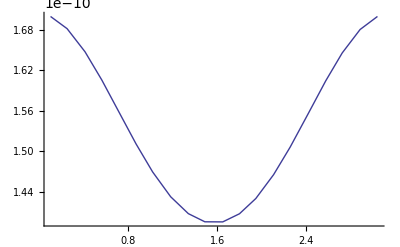

```mathematica
With[{ω=1.1},
Plot[Re[dσdΩFull[1/137.,4 ω^2,-2 ω^2 (1-Cos[θ]),1.0]],{θ,.1,π-.1},PlotRange->{{0,π},{2*10^-10,1*10^-10}},AxesOrigin->{0,1*10^-10},PlotPoints->20,MaxRecursion->0]
]
```

The reason for the long evaluation time is due to numerous calls to the complicated special functions ScalarC0, and especially ScalarD0 for each kinematic point.  The evaluation time can be improved if the function is organized so that each special function appears once in the expression.

There are 5562 instances of ScalarC0 and ScalarD0 each in ampSqFull:

```mathematica
Count[ampSqFull,_ScalarC0,Infinity]
Count[ampSqFull,_ScalarD0,Infinity]
```

5562

5562

Collect the squared amplitude by the special functions, and simplify each coefficient (25 seconds runtime).  There are now only 33 instances of the special functions:

```mathematica
ampSqFullImpr=Collect[ampSqFull,{_DiscB,_ScalarC0,_ScalarD0,_Conjugate},Simplify];
Count[ampSqFullImpr,_ScalarC0,Infinity]
Count[ampSqFullImpr,_ScalarD0,Infinity]
```

33

33

Construct the differential cross section, and plot it (1 second runtime):

```mathematica
dσdΩFull[α_,s_,t_,m_]=1/(2s)ampSqFullImpr 1/(32 π^2)/.e->√(α 4π);
```

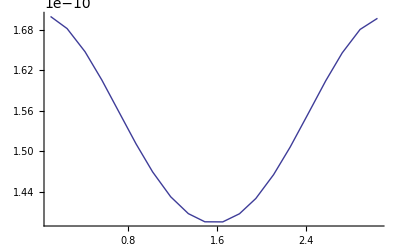

```mathematica
With[{ω=1.1},
Plot[Re[dσdΩFull[1/137.,4 ω^2,-2 ω^2 (1-Cos[θ]),1.0]],{θ,.1,π-.1},PlotRange->{{0,π},{2*10^-10,1*10^-10}},AxesOrigin->{0,1*10^-10},PlotPoints->20,MaxRecursion->0]
]
```

To avoid having to recalculate and simplify the differential cross section each time Mathematica is restarted, it is useful to save it to disk with DumpSave.  The definition can then be loaded with Get when needed across separate sessions.

Save the definition of dσdΩFull in a binary file:

```mathematica
SetDirectory[$TemporaryDirectory];
DumpSave["QED-LBL-ampSq.mx",dσdΩFull];
```

Load the definitions in "QED-LBL-ampSq.mx":

```mathematica
SetDirectory[$TemporaryDirectory];
Get["QED-LBL-ampSq.mx"];
```

More About

Package-X

Related Tutorials

Bringing the Arguments of D functions to Canonical Form